-Graphics-

Narcissistic Numbers

Students

Baskaya, Semi Kaan, Student-ID, s_baskaya23@stud.hwr-berlin.de

Busson, Jan, Student-ID, s_busson23@stud.hwr-berlin.de

Haaken, Jan, Student-ID, xxx.xxx@xxx.de

Lecture		Optimization and Data Analytics

Lecturer		Prof. Dr. Frank Brand

## Content Overview

Statutory Declaration

1 Problem Statement

2 Solution     xx

2.1 xxx     xx

2.2 xxx     xx

2.3 xxx     xx

3 Sensitivity Analysis     xx

3.1 xxx     xx

3.2 xxx     xx

3.3 xxx     xx

4 Possible Generalizations of the Problem

5 Summary of results

## Statutory Declaration

I hereby formally declare that we have written the submitted term paper entirely by ourselves without anyone else’s assistance. Wherever we have drawn on literature or other sources, either in direct quotes or in paraphrasing such material, we have given the reference to the original author or authors and to the source where it appeared. We are aware that the use of quotations, or close paraphrasing, from books, magazines, newspapers, the internet, or other sources, which are not marked as such, will be considered an attempt at deception, and that the term paper will be graded with a fail. We are aware of the fact, that the use of Large Language Models (LLM) like ChatGPT or others without a quotation will be graded with a fail, too.

____________________

Location / Date

-Graphics-

Signature

-Graphics-

Signature

___________________________

Signature

## 1. Problem Statement

Goal: Find as many Narcissistic Numbers as possible

Definition: A number that can be recreated by summing each of their digits raised to the power of the total number of digits in the number itself.

Example: 153 = 1^3+5^3+3^3 (Note: 153 = 1 + 125 + 27)

Qualitity Function:

```mathematica
QF[n_]:=(n-Sum[IntegerDigits[n][[i]]^IntegerLength[n],{i,1,IntegerLength[n]}])^2
```

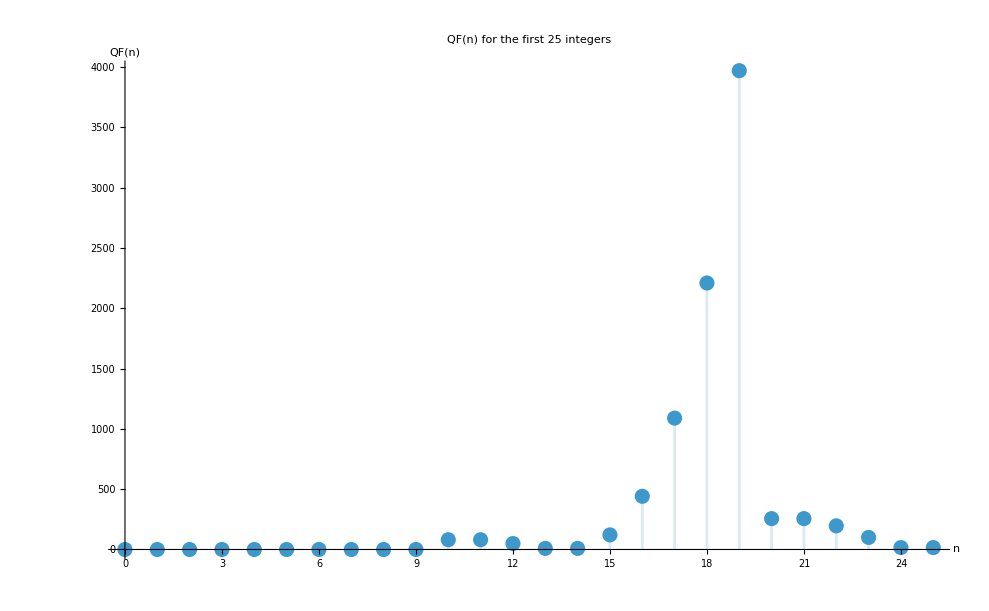

```mathematica
Show[DiscretePlot[QF[n],{n,0,25},AxesLabel->{"n","QF(n)"},PlotLabel->"QF(n) for the first 25 integers"],PlotRange->Full]
```

## 2. Solution

```mathematica
maxdimension = 6;
```

The following function returns all narcissistic numbers in an interval and  the time required for the calculation .

```mathematica
returnNarcissisticRange[lower_,upper_]:=Module[{time,numbers},{time,numbers}=AbsoluteTiming[Select[Range[lower,upper],QF[#]==0&]];
{numbers,time}]
```

### 2.1 Brute force

Brute force describes an algorithmic approach in which all possible candidates are tested until a solution is found. 

Since this method does not use any filtering or optimization strategies, it is computationally more expensive than more advanced algorithms.

In this case, the brute force approach checks every number within the given range. For each number, the quality function is evaluated in order to determine whether the number is narcissistic or not.

```mathematica
rows=Table[Module[{lower,upper,numbers,time},upper=10^k;
lower=If[k==0,0,10^(k-1)+1];
{numbers,time}=returnNarcissisticRange[lower,upper];
{Superscript[10,k],Row[numbers,"; "],NumberForm[time,{Infinity,6}]}],{k,0,maxdimension}];

Grid[Prepend[rows,{"Upper bound","Numbers","Time in seconds"}],Frame->All]
```

The following table shows the narcissistic numbers found within each power-of-10 range, together with the corresponding computation time.

```mathematica
{{"Upper bound", "Numbers", "Time in seconds"}, {10^0, ; "; "01, "0.000085"}, {10^1, ; "; "23456789, "0.000121"}, {10^2, ; "; ", "0.001822"}, {10^3, ; "; "153370371407, "0.018136"}, {10^4, ; "; "163482089474, "0.207681"}, {10^5, ; "; "547489272793084, "2.399109"}, {10^6, ; "; "548834, "27.720764"}}
```

The brute force approach is simple and useful as a baseline, but it does not scale well because every number has to be checked individually.

### 2.2 Brute force parallelized

The brute force approach can be improved by parallelizing the evaluation of the candidate numbers. Since the quality function can be applied to each number independently, the search range is distributed across multiple Mathematica subkernels using ParallelTable. Each candidate number is tested by evaluating QF[n], and numbers with QF[n] = 0 are identified as narcissistic numbers.

Although this reduces the computation time, the algorithm still checks every number in the given range. Therefore, the parallelized brute force approach improves practical runtime but does not solve the scalability problem of the original brute force method.

The following table shows the narcissistic numbers found up to each upper bound and the corresponding computation time of the parallelized brute force implementation.

```mathematica
Clear[dimensionRange]

dimensionRange[d_Integer]:=If[d==1,{0,9},{10^(d-1),10^d-1}]

maxdimensionParallelBF=6;
```

```mathematica
Clear[returnNarcissisticParallelRange]

returnNarcissisticParallelRange[lower_Integer,upper_Integer]:=Module[{time,numbers},If[$KernelCount==0,LaunchKernels[]];
DistributeDefinitions[F,QF];
{time,numbers}=AbsoluteTiming[ParallelTable[If[QF[i]==0,i,Nothing],{i,lower,upper},Method->"CoarsestGrained"]];
{numbers,time}]
```

```mathematica
rows=Table[Module[{lower,upper,numbers,time},{lower,upper}=dimensionRange[d];
{numbers,time}=returnNarcissisticParallelRange[lower,upper];
{d,Row[{lower," - ",upper}],Row[numbers,"; "],NumberForm[time,{Infinity,3}]}],{d,1,maxdimensionParallelBF}];

Grid[Prepend[rows,{"Digit length","Search range","Numbers","Time in seconds"}],Frame->All]
```

Digit length | Search range | Numbers | Time in seconds
1 | 0 - 9 | ; ; 0123456789 | 0.122
2 | 10 - 99 | ; ;  | 0.012
3 | 100 - 999 | ; ; 153370371407 | 0.032
4 | 1000 - 9999 | ; ; 163482089474 | 0.087
5 | 10000 - 99999 | ; ; 547489272793084 | 0.549
6 | 100000 - 999999 | ; ; 548834 | 5.860

```mathematica
CloseKernels[]
```

{Local,Local,Local,Local,Local,Local}

The results show that parallelization significantly improves the runtime compared to the sequential brute force approach. Since the evaluation of each candidate number is independent, the workload can be distributed effectively across multiple Mathematica subkernels.

However, the underlying algorithmic structure remains unchanged. Even in the parallelized version, every number in the search range is still checked individually. Therefore, parallelization reduces the practical computation time, but it does not remove the fundamental scalability limitation of the brute force method.

### 2.3 Digit Permutation Class Approach

A limitation of the brute force approach is that it checks numbers individually, even if several numbers consist of the same digits in a different order.

For Example 153, 315 and 531 have the same digit composition. Therefore, they also have the same digit power sum.

Corresponding Digit vector:
{0, 1, 0, 1, 0, 1, 0, 0, 0, 0}

```mathematica
digitVector[n_]:=Table[Count[IntegerDigits[n],d],{d,0,9}]
```

Based on this digit vector, the narcissistic sum can be calculated once for the whole permutation class. All numbers with the same digit vector produce the same sum.

```mathematica
digitVectorsOfLength[digits_]:=FrobeniusSolve[ConstantArray[1,10],digits]
permutationClassVectorPowerSum[v_]:=Module[{digits},digits=Total[v];
Sum[v[[d+1]]*d^digits,{d,0,9}]]
```

Instead of checking every number individually, each digit composition is evaluated only once.

- For each digit vector, the corresponding power sum is calculated.

- This power sum is the only possible candidate that can be narcissistic for this digit composition.

- The candidate is accepted only if its digit vector matches the original digit vector and if it lies within the selected range.

```mathematica
rows=Table[Module[{lower,upper,numbers,time},upper=10^k;
lower=If[k==0,0,10^(k-1)+1];
{numbers,time}=returnNarcissisticPermutationRange[lower,upper];
{Superscript[10,k],Row[numbers,"; "],NumberForm[time,{Infinity,6}]}],{k,0,maxdimension}];

Grid[Prepend[rows,{"Upper bound","Numbers","Time in seconds"}],Frame->All]
```

```mathematica
{{"Upper bound", "Numbers", "Time in seconds"}, {10^0, ; "; "01, "0.020393"}, {10^1, ; "; "23456789, "0.004445"}, {10^2, ; "; ", "0.020456"}, {10^3, ; "; "153370371407, "0.075776"}, {10^4, ; "; "163482089474, "0.227301"}, {10^5, ; "; "547489272793084, "0.493498"}, {10^6, ; "; "548834, "1.129639"}}
```

The results show that parallelization does not automatically lead to faster runtimes for small search ranges. This is because starting kernels, distributing definitions, and coordinating parallel tasks introduces additional overhead.

### 2.4 Digit Permutation Class Approach parallelized

A further optimization is to parallelize this process. Since each digit composition can be evaluated independently, the workload can be distributed across multiple processor cores. This means that several digit classes are checked at the same time instead of being processed sequentially.

```mathematica
LaunchKernels[];

DistributeDefinitions[digitVector,digitVectorsOfLength,permutationClassVectorPowerSum]
```

LaunchKernels::nodef: Some parallel subkernels are already running. Not launching default kernels again.

{digitVector,digitVectorsOfLength,permutationClassVectorPowerSum}

```mathematica
returnNarcissisticPermutationRangeParallel[lower_,upper_]:=Module[{time,numbers,minDigits,maxDigits,vectors},If[$KernelCount==0,LaunchKernels[]];
DistributeDefinitions[digitVector,digitVectorsOfLength,permutationClassVectorPowerSum];
minDigits=Max[1,IntegerLength[lower]];
maxDigits=IntegerLength[upper];
{time,numbers}=AbsoluteTiming[vectors=Join@@Table[digitVectorsOfLength[d],{d,minDigits,maxDigits}];
numbers=ParallelTable[Module[{value},value=permutationClassVectorPowerSum[v];
If[lower<=value<=upper&&digitVector[value]==v,value,Nothing]],{v,vectors}];
Sort[DeleteDuplicates[numbers]]];
{numbers,time}]
```

The following table applies the parallelized digit permutation class approach to increasing upper bounds. For each upper bound, the table shows the narcissistic numbers found in the corresponding range and the computation time required.

```mathematica
rows=Table[Module[{lower,upper,numbers,time},upper=10^k;
lower=If[k==0,0,10^(k-1)+1];
{numbers,time}=returnNarcissisticPermutationRangeParallel[lower,upper];
{Superscript[10,k],Row[numbers,"; "],NumberForm[time,{Infinity,6}]}],{k,0,maxdimension}];

Grid[Prepend[rows,{"Upper bound","Numbers","Time in seconds"}],Frame->All]
```

Upper bound | Numbers | Time in seconds
10^0 | ; ; 01 | 0.081113
10^1 | ; ; 23456789 | 0.027802
10^2 | ; ;  | 0.042369
10^3 | ; ; 153370371407 | 0.087159
10^4 | ; ; 163482089474 | 0.292913
10^5 | ; ; 547489272793084 | 0.683302
10^6 | ; ; 548834 | 1.153338

Parallelization does not automatically lead to faster runtimes. It is only useful when the workload is large enough to compensate for the overhead.

## 3 Sensitivity Analysis

The previous chapter introduced several algorithmic approaches for identifying narcissistic numbers. These approaches differ in how they handle the search space and how much redundant computation they avoid. However, runtime performance is not only determined by the algorithm itself, but also by input size, digit length, implementation details, and the use of parallelization.

The purpose of this sensitivity analysis is therefore to examine how strongly the computation time reacts to changes in selected parameters. In this notebook, the most relevant parameter is the digit dimension of the search interval. Increasing the number of digits directly increases the number of candidate numbers in the brute force approach. In contrast, the digit permutation class approach reacts differently, because it operates on digit compositions instead of individual numbers.

Furthermore, the sensitivity analysis investigates whether parallelization consistently improves runtime. Since parallelization introduces overhead through kernel startup, task distribution, and result collection, it is not guaranteed to be faster for small search spaces. The analysis therefore helps to identify under which conditions each approach becomes efficient.

### 3.1 Sensitivity to Search Dimensions

The first sensitivity parameter is the digit length of the search interval. This parameter has a direct effect on the size of the search space. In the brute force approach, every number in the interval has to be checked individually. Therefore, the number of candidates grows exponentially with the digit length.

For a fixed digit length d, there are 9 * 10^(d - 1) positive d-digit numbers. This explains why the brute force approach quickly becomes infeasible for larger dimensions.

The digit permutation class approach is less sensitive to the raw number of candidates. Instead of evaluating every number, it evaluates possible digit compositions. The number of digit compositions of length d corresponds to the number of non-negative integer solutions of x0 + x1 + ... + x9 = d, which is Binomial[d + 9, 9]. Although this number also increases, it grows much more slowly than the full brute force search space.

The following table compares the number of candidates that have to be evaluated by the brute force approach with the number of digit permutation classes for each digit length. The reduction factor shows how many times larger the brute force search space is compared to the digit class search space.

```mathematica
Clear[candidateCount,digitClassCount]

candidateCount[d_]:=If[d==1,10,9*10^(d-1)]

digitClassCount[d_]:=Binomial[d+9,9]

complexityRows=Table[{d,candidateCount[d],digitClassCount[d],NumberForm[N[candidateCount[d]/digitClassCount[d]],{Infinity,2}]},{d,1,maxdimension}];

Grid[Prepend[complexityRows,{"Digit length","Brute force candidates","Digit classes","Reduction factor"}],Frame->All]
```

Digit length | Brute force candidates | Digit classes | Reduction factor
1 | 10 | 10 | 1.00
2 | 90 | 55 | 1.64
3 | 900 | 220 | 4.09
4 | 9000 | 715 | 12.59
5 | 90000 | 2002 | 44.96
6 | 900000 | 5005 | 179.82

The table shows that both approaches start with the same number of objects for one-digit numbers. However, as the digit length increases, the number of brute force candidates grows much faster than the number of digit classes. The reduction factor therefore increases with each additional digit, showing that the digit permutation class approach becomes increasingly more efficient for larger search dimensions. This explains why reducing the search space is more important than simply evaluating the original brute force search faster.

The following logarithmic plot visualizes how the search space changes with increasing digit length. It compares the growth of brute force candidates with the growth of digit permutation classes.

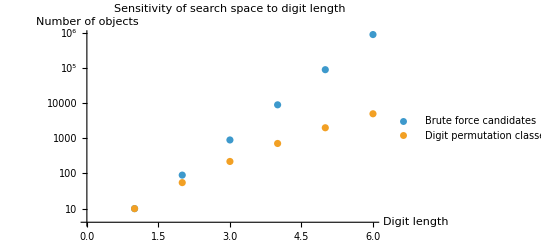

```mathematica
ListLogPlot[{Table[{d,candidateCount[d]},{d,1,maxdimension}],Table[{d,digitClassCount[d]},{d,1,maxdimension}]},PlotLegends->{"Brute force candidates","Digit permutation classes"},AxesLabel->{"Digit length","Number of objects"},PlotLabel->"Sensitivity of search space to digit length"]
```

The plot confirms the different growth behavior of the two approaches. The number of brute force candidates grows exponentially with the digit length, which appears as a straight line on the logarithmic scale. In contrast, the number of digit permutation classes grows much more slowly. This visualizes why the brute force approach becomes increasingly sensitive to digit length, while the digit permutation class approach is less affected by larger search dimensions.

### 3.2 Sensitivity to Algorithmic Approach

The second sensitivity analysis compares the runtime behavior of the different algorithmic approaches. To make the comparison fair, all approaches are applied to the same digit intervals. This means that for each digit length d, only numbers with exactly d digits are considered.

This avoids repeatedly recalculating smaller numbers and allows the marginal runtime increase per digit dimension to be observed more clearly. The comparison shows how sensitive each algorithm is to an increase in the size of the search space.

The expectation is that the brute force methods will show the strongest runtime increase, because they process every candidate number individually. The digit permutation class approaches should be less sensitive to the digit length, since they operate on digit vectors instead of individual numbers.

The following table compares the runtime behavior of the implemented approaches for fixed digit intervals. Each method is executed several times, and the table reports the mean runtime, standard deviation, number of completed runs, and number of narcissistic numbers found.

```mathematica
Clear[measureRuntime,formatRuntimeRow]

measureRuntime[name_,func_,d_Integer,repetitions_:3,timeLimit_:120]:=Module[{lower,upper,runs,successfulRuns,times,nums,t},{lower,upper}=dimensionRange[d];
runs=Table[TimeConstrained[{nums,t}=func[lower,upper];
{nums,t},timeLimit,$Failed],{repetitions}];
successfulRuns=DeleteCases[runs,$Failed];
If[successfulRuns==={},{name,d,lower,upper,0,Missing["Timeout"],Missing["NotAvailable"],Missing["NotAvailable"]},times=successfulRuns[[All,2]];
{name,d,lower,upper,Length[successfulRuns],Mean[times],If[Length[times]>1,StandardDeviation[times],0],Length[First[successfulRuns][[1]]]}]]

formatRuntimeRow[row_]:=Module[{name,d,lower,upper,completed,mean,sd,found},{name,d,lower,upper,completed,mean,sd,found}=row;
{name,d,Row[{lower," - ",upper}],completed,If[Head[mean]===Missing,"timeout",NumberForm[mean,{Infinity,6}]],If[Head[sd]===Missing,"-",NumberForm[sd,{Infinity,6}]],If[Head[found]===Missing,"-",found]}]
```

```mathematica
settings={{"Brute force",returnNarcissisticRange,Range[1,6]},{"Parallel brute force",returnNarcissisticParallelRange,Range[1,7]},{"Digit permutation class",returnNarcissisticPermutationRange,Range[1,maxdimension]},{"Parallel digit permutation class",returnNarcissisticPermutationRangeParallel,Range[1,maxdimension]}};

repetitions=3;

runtimeRows=Flatten[Table[Table[measureRuntime[setting[[1]],setting[[2]],d,repetitions,120],{d,setting[[3]]}],{setting,settings}],1];

Grid[Prepend[formatRuntimeRow/@runtimeRows,{"Method","Digits","Range","Completed runs","Mean time","Std. dev.","Numbers found"}],Frame->All]
```

Method | Digits | Range | Completed runs | Mean time | Std. dev. | Numbers found
Brute force | 1 | 0 - 9 | 3 | 0.000131 | 0.000037 | 10
Brute force | 2 | 10 - 99 | 3 | 0.001269 | 0.000016 | 0
Brute force | 3 | 100 - 999 | 3 | 0.019047 | 0.002127 | 4
Brute force | 4 | 1000 - 9999 | 3 | 0.207915 | 0.001106 | 3
Brute force | 5 | 10000 - 99999 | 3 | 2.400638 | 0.076977 | 3
Brute force | 6 | 100000 - 999999 | 3 | 26.600591 | 0.297406 | 1
Parallel brute force | 1 | 0 - 9 | 3 | 0.009372 | 0.000559 | 10
Parallel brute force | 2 | 10 - 99 | 3 | 0.008934 | 0.000514 | 0
Parallel brute force | 3 | 100 - 999 | 3 | 0.039082 | 0.010829 | 4
Parallel brute force | 4 | 1000 - 9999 | 3 | 0.065809 | 0.008442 | 3
Parallel brute force | 5 | 10000 - 99999 | 3 | 0.534449 | 0.008066 | 3
Parallel brute force | 6 | 100000 - 999999 | 3 | 5.652886 | 0.043233 | 1
Parallel brute force | 7 | 1000000 - 9999999 | 3 | 64.312333 | 1.828620 | 4
Digit permutation class | 1 | 0 - 9 | 3 | 0.001116 | 0.000101 | 10
Digit permutation class | 2 | 10 - 99 | 3 | 0.004747 | 0.000371 | 0
Digit permutation class | 3 | 100 - 999 | 3 | 0.017259 | 0.000063 | 4
Digit permutation class | 4 | 1000 - 9999 | 3 | 0.057493 | 0.001192 | 3
Digit permutation class | 5 | 10000 - 99999 | 3 | 0.209313 | 0.009826 | 3
Digit permutation class | 6 | 100000 - 999999 | 3 | 0.441430 | 0.006210 | 1
Parallel digit permutation class | 1 | 0 - 9 | 3 | 0.010240 | 0.000669 | 10
Parallel digit permutation class | 2 | 10 - 99 | 3 | 0.016792 | 0.000697 | 0
Parallel digit permutation class | 3 | 100 - 999 | 3 | 0.038135 | 0.001962 | 4
Parallel digit permutation class | 4 | 1000 - 9999 | 3 | 0.070674 | 0.002321 | 3
Parallel digit permutation class | 5 | 10000 - 99999 | 3 | 0.260767 | 0.015450 | 3
Parallel digit permutation class | 6 | 100000 - 999999 | 3 | 0.563392 | 0.019538 | 1

The results show that the sequential brute force approach has the strongest increase in runtime as the digit length grows. Parallel brute force improves the runtime for larger digit lengths, but it still has to evaluate every candidate number individually. The digit permutation class approach is clearly more efficient for higher dimensions, because it avoids redundant calculations for numbers with the same digit composition. The parallel digit permutation class approach does not outperform the non-parallel version in these smaller dimensions, which indicates that the overhead of parallelization is still too large compared to the workload.

The following logarithmic plot visualizes the mean runtime of the different approaches by digit length. This makes it easier to compare the growth behavior of the algorithms across several orders of magnitude.

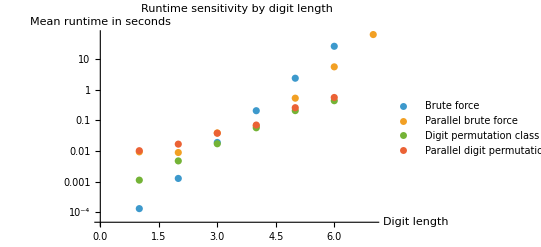

```mathematica
runtimePlotData=Table[With[{method=settings[[i,1]]},Cases[runtimeRows,row_/;row[[1]]==method&&NumericQ[row[[6]]]:>{row[[2]],row[[6]]}]],{i,Length[settings]}];

ListLogPlot[runtimePlotData,PlotLegends->settings[[All,1]],AxesLabel->{"Digit length","Mean runtime in seconds"},PlotLabel->"Runtime sensitivity by digit length"]
```

The plot shows that the brute force methods become increasingly expensive as the digit length grows. Parallel brute force reduces the runtime compared to the sequential brute force method for larger dimensions, but the overall growth trend remains similar. The digit permutation class approaches show a much flatter runtime increase, which demonstrates their lower sensitivity to the size of the original search space. For the tested dimensions, the non-parallel digit permutation class approach performs best overall.

### 3.3 Sensitivity to Parallelization

The third sensitivity parameter is the degree of parallelization. Parallel execution can reduce runtime when the workload is large enough to compensate for the overhead of managing multiple kernels. However, for small search spaces, this overhead can dominate the actual computation time.

The results indicate that parallelization is not universally beneficial. Especially for smaller digit dimensions, the non-parallel digit permutation class approach can be faster because it avoids kernel startup and communication overhead. For larger dimensions, parallelization may become more useful, but this depends on the number of available processor cores and the size of the generated digit vector list.

Therefore, the sensitivity analysis shows that parallelization should not be treated as an automatic optimization. It is only advantageous when the computational workload per parallel task is sufficiently large.

The following table investigates how the runtime of the parallel digit permutation class approach changes when the number of Mathematica kernels is varied. The test is performed for digit length 10 in order to create a workload that is large enough for parallelization to become relevant.

```mathematica
Clear[kernelSensitivityRows]

testDimension=10;
kernelCounts=Range[1,Min[6,$ProcessorCount]];

kernelSensitivityRows=Table[CloseKernels[];
LaunchKernels[kernels];
{numbers,time}=returnNarcissisticPermutationRangeParallel@@dimensionRange[testDimension];
{kernels,testDimension,NumberForm[time,{Infinity,6}],Length[numbers]},{kernels,kernelCounts}];

CloseKernels[];

Grid[Prepend[kernelSensitivityRows,{"Kernels","Digit length","Time in seconds","Numbers found"}],Frame->All]
```

Kernels | Digit length | Time in seconds | Numbers found
1 | 10 | 12.709578 | 1
2 | 10 | 8.968192 | 1
3 | 10 | 7.410488 | 1
4 | 10 | 6.601881 | 1
5 | 10 | 6.279947 | 1
6 | 10 | 5.934793 | 1

## 3 Possible Generalizations of the Problem

The concept of narcissistic numbers can be extended in several ways.

Narcissistic numbers with different bases.

62_10 = 332_4, we can say: 3^3 + 3^3 + 2^3 = 62  

So 62_10 is a narcissistic number in base 4.

Narcissistic numbers with a different definition.

Narcissistic numbers with increasing exponents: 2427 = 2^1 + 4^2+ 2^3 + 7^4 = 2 + 16 + 8 + 2401 = 2427

Narcissistic numbers with constant base: 4624 = 4^4+ 4^6 + 4^2+ 4^4 = 256 + 4096 + 16 + 256 = 4624

Factorion Numbers: 145 = 1! + 4! + 5! = 1 + 24 + 120 = 145

-> With minor adjustments our approaches can also be applied to these types of narcissistic numbers

## 4 Summary of results

This project investigated different algorithmic approaches for identifying narcissistic numbers in base 10.

The brute force approach is simple and transparent, but it becomes inefficient as the digit length increases.

The digit permutation class approach provides the main algorithmic improvement by avoiding redundant calculations.

Parallelization can further improve runtime, but only for sufficiently large workloads.

The best strategy is to group numbers by digit vectors, evaluate each digit composition once, and apply parallelization for larger workloads.